# Srednješolsko izobraževanje v RS

V nalogi analiziram podatke, ki ponazarjajo število vpisanih dijakov po posameznih stopnjah srednješolskega izobraževanja glede na spol in starost v zadnjih dvanajstih letih. Podatke pridobim iz SURS-a. Analizirani podatki so:
-vrsta oz. stopnja izobraževanja,
-spol
- šolsko leto
Podatke sem primerjal vertiaklno(po šolskih letih) in horizontalno(spol,stopnja)
Poudarek analize je na gimnazijskem programu.
Primerjave bom prikazal na več načinov in interpretiral.

## 1. PRIMERJAVA: Število vpisanih po letih

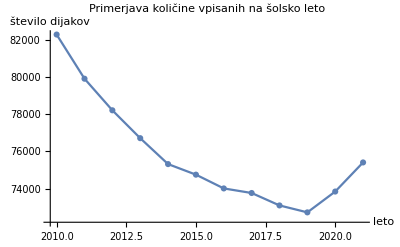

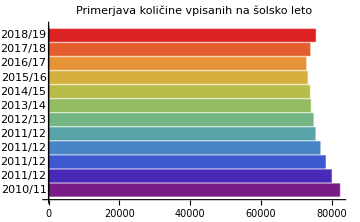

```mathematica
skupni = Import[NotebookDirectory[]<> "Skupaj vpisi.xlsx","Dataset", CharacterEncoding->"WindowsEastEurope"]//First;

ListLinePlot[skupni//Query[3,4;;15], 
PlotMarkers->Automatic,
AxesLabel->{"leto","število dijakov"},
DataRange->{2010,2021},
PlotLabel->"Primerjava količine vpisanih na šolsko leto"]

BarChart[skupni//Query[3,4;;15], ChartLabels->{"2010/11","2011/12","2011/12","2011/12","2011/12","2012/13","2013/14","2014/15","2015/16","2016/17","2017/18","2018/19","2019/20","2020/21","2021/22"},
PlotLabel->"Primerjava količine vpisanih na šolsko leto", 
ChartStyle -> "Rainbow", ImageSize -> Medium, BarOrigin->Left]
```

Interpretacija prikaza:
Primerjal sem število vpisanih srednješolcev glede na posamezno šolsko leto. Ugotovil sem, da je bilo največ dijakov v šolskem letu 2010/11. Po tem letu je bilo vsako leto manj dijakov, najmanj leta 2016/17. V zadnjih petih letih vpis srednješolcev znova narašča.
Podatki so prikazani na 2 načina, Vendar se mi zdi prvi način bolj pregleden, najvrjetneje zaradi manjšega razpona na vertikalni osi.

## 2. PRIMERJAVA: Razmerje vpisanih glede na program

```mathematica
programi = Import[NotebookDirectory[]<> "vsi programi.xlsx","Dataset", CharacterEncoding->"WindowsEastEurope"]//First;


PieChart[{
programi // Query[3,4;;15]// Total,
programi // Query[4,4;;15]// Total,
programi // Query[5,4;;15]// Total,
programi // Query[9,4;;15]// Total
},
PlotLabel->"Primerjava količine vpisanih glede na smer",
ChartLegends->{"Nižje poklicno","Srednje poklicno", "Srednje tehniško in drugo strokovno", "Srednje splošno"},
ChartStyle->{Red, Green, Blue, Yellow}]
```

-Graphics-

Interpretacija prikaza:
Najmanj dijakov se vpisuje v nižje poklicno izobraževanje(dve in tri letni program), največ pa v srednje tehniške in druge strokovne šole. Dijakov teh šol je skoraj polovica vseh vpisanih srednješolcev v zadnjih dvanajstih letih. Približno tretjino je tudi gimnazijcev. Sklepam, da je število vpisnih mest odvisno glede na potrebe gospodarstva in drugih sektorjev v državi.

## 3. PRIMERJAVA: Nihanje števila vpisanih za posamezne smeri v vsakem letu

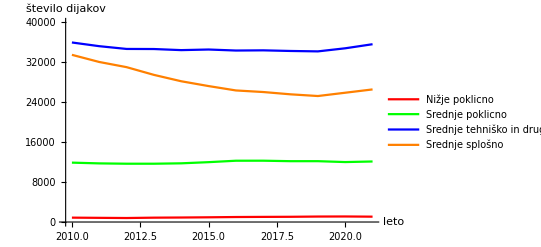

```mathematica
Show[n = ListLinePlot[programi // Query[3,4;;15],
PlotLegends->  LineLegend[{"Nižje poklicno"} ],
 PlotStyle->Red,
PlotRange->{0,40000},DataRange->{2010,2021}
],

sp = ListLinePlot[programi // Query[4,4;;15],
PlotLegends->  LineLegend[{"Srednje poklicno"} ],
 PlotStyle->Green,
PlotRange->{0,40000},DataRange->{2010,2021}
],

st = ListLinePlot[programi // Query[5,4;;15],
PlotLegends->  LineLegend[{"Srednje tehniško in drugo strokovno"} ],
 PlotStyle->Blue,
PlotRange->{0,40000},DataRange->{2010,2021}
],

ss = ListLinePlot[programi // Query[9,4;;15],
PlotLegends->  LineLegend[{"Srednje splošno"} ], 
PlotStyle->Orange,
PlotRange->{0,40000},DataRange->{2010,2021}
],AxesLabel->{"leto","število dijakov"}

]
```

Interpretacija prikaza:
Iz grafa je zelo očitno kako malo je vpisanih dijakov v Nižje poklicnem izobraževanju glede na ostale stopnje, kar sem ugotovil že v prejšnji primerjavi z drugačnim prikazom. Primerjava po letih pokaže, da se je najbolj spreminjalo število vpisanih gimnazijcev(Srednje splošno). V ostalih programih je bil vpis skozi leta skoraj konstanten. V vseh letih je največ vpisanih na srednejm stehničnem in drugem strokovnem izobraževanju, le v letu 2010/11 je bilo vpisov v srednje splošno in srednje tehniško skoraj enako(razlika le okoli 2000).

## 4. PRIMERJAVA: Razmerje po spolu glede na vrsto izobraževanja

```mathematica
moskiinzenske = Import[NotebookDirectory[]<> "moski zenske.xlsx","Dataset", CharacterEncoding->"WindowsEastEurope"]//First;
 
PieChart[{{
(moskiinzenske// Query[3,4]) + (moskiinzenske// Query[3,6]),
( moskiinzenske// Query[3,5]) + ( moskiinzenske// Query[3,7])
},
{
(moskiinzenske// Query[4,4]) + (moskiinzenske// Query[4,6]),
(moskiinzenske// Query[4,5]) + (moskiinzenske// Query[4,7])
},
{
(moskiinzenske// Query[5,4]) + ( moskiinzenske// Query[5,6]),
(moskiinzenske// Query[5,5]) + (moskiinzenske// Query[5,7])
},
{
(moskiinzenske// Query[6,4]) + (moskiinzenske// Query[6,6]),
(moskiinzenske// Query[6,5]) + (moskiinzenske// Query[6,7])
}},
PlotLabel->"Primerjava količine vpisanih na posamezen program glede na spol",
ChartLayout->"Grouped",
ChartLabels->{{"NP","SP","ST","GIM"}, None},
 SectorSpacing->1,
ChartLegends -> {"Moški", "Ženske"},
ImageSize-> Large,
ChartStyle->{ Blue,Magenta}]
```

-Graphics-

Interpretacija prikaza:
Iz prikaza lahko razberemo, da je največji delež moških v nižje poklicnem izobraževanju. Skoraj enak delež je tudi v srednej poklicnem, kar dokazuje, da se moški bolj zanimajo za “praktične” poklice, ki se po srednji šoli že zaključijo in nadaljevanje študija na fakulteti ni nujno.
Skoraj dve tretjini vpisanih na gimnazije so dekleta. Menim, da je več deklet pripravljenih dlje študirati, saj gimnazijski program ne daje dokončne izobrazbe(gimnazijski maturant).

## 5. PRIMERJAVA: Število vpisnih v prvi letnik gimnazije po letih

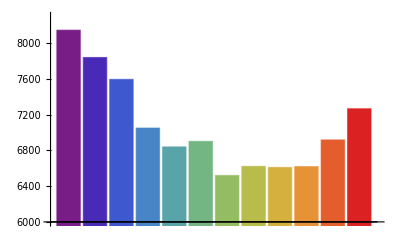

7077.75

```mathematica
gim1letnik = Import[NotebookDirectory[]<> "gim_1letnik.xlsx","Dataset", CharacterEncoding->"WindowsEastEurope"]//First;

BarChart[gim1letnik // Query[3,4;;15], PlotRange->{6000,8300}, ChartStyle-> "Rainbow"]
(gim1letnik // Query[3,4;;15]//Total ) / 12
```

Interpretacija prikaza:
Največ vpisanoh v prvi letnik  gimnazije je bilo v šolskem letu 2010/11, nato je vpis na ta program začel padati. Najmanj gimnazijcev je bilo v prvem letniku v šolskem letu 2016/17, kar za 1600 dijakov manj kot v letu 2010/11. V naslednjih letih je bil vpis konstanten, nato pa znova začel naraščati, ko je v letu 2021/21 dosegel skoraj 7300 dijakov. Kar je malo nad povprečjem vpisanih prvošolcev v zadnjih dvanajstih letih(povp. 7100).

```mathematica
ClearAll
```

ClearAll

## 6. PRIMERJAVA: Razmerje starosti dijakov od leta 2017/18 dalje

```mathematica
gimStarost = Import[NotebookDirectory[]<> "gim_starost.xlsx","Dataset", CharacterEncoding->"WindowsEastEurope"]//First;
ClearAll


PieChart[{
{
gimStarost//Query[2,11],
gimStarost//Query[3,11],
gimStarost//Query[4,11],
gimStarost//Query[5,11],
gimStarost//Query[6,11],
gimStarost//Query[7,11],
gimStarost//Query[8,11],
gimStarost//Query[9,11]

},
{gimStarost//Query[2,12],
gimStarost//Query[3,12],
gimStarost//Query[4,12],
gimStarost//Query[5,12],
gimStarost//Query[6,12],
gimStarost//Query[7,12],
gimStarost//Query[8,12],
gimStarost//Query[9,12]
},
{gimStarost//Query[2,13],
gimStarost//Query[3,13],
gimStarost//Query[4,13],
gimStarost//Query[5,13],
gimStarost//Query[6,13],
gimStarost//Query[7,13],
gimStarost//Query[8,13],
gimStarost//Query[9,13]
},
{gimStarost//Query[2,14],
gimStarost//Query[3,14],
gimStarost//Query[4,14],
gimStarost//Query[5,14],
gimStarost//Query[6,14],
gimStarost//Query[7,14],
gimStarost//Query[8,14],
gimStarost//Query[9,14]
},
{gimStarost//Query[2,15],
gimStarost//Query[3,15],
gimStarost//Query[4,15],
gimStarost//Query[5,15],
gimStarost//Query[6,15],
gimStarost//Query[7,15],
gimStarost//Query[8,15],
gimStarost//Query[9,15]
}
},
ChartLayout->"Grouped",
PlotLabel->"Razmerje starosti dijakov od leta 2017/18 dalje",
ChartLegends -> {"14 let","15 let","16 let","17 let","18 let","19 let","20 let","21 let in več"},
ChartStyle->{ Cyan, Magenta,Green,Red,Orange,Yellow,Pink,Blue}]
```

ClearAll

-Graphics-

Interpretacija prikaza:
Kot je pričakovano je največ dijakov v starostni skupini od 15 do 18 let(enakomerna razporeditev po letih). Nekaj dijakov je starih tudi 19 kar lahko sklepamo da so ti dijako kakšno leto ponavljali ali šli kasneje v šolo. Zelo malo je dijakov mlajših od 15 let, saj le redko kdo zaključi osnovno šolo prej(preskočijo razred ali pa gredo prej v šolo). Nekaj diajkov je starih tudi 20 let ali več, predvidevam da so to dijaki, ki so vpisani v maturitetni tečaj in gimnazijskega izobraževanja niso prej zaključili.